```mathematica
assump=k>0&&m>0&&ℏ>0&&ℰ>0&&A>0&&B>0&&α>0&&β>0
```

k>0&&m>0&&ℏ>0&&ℰ>0&&A>0&&B>0&&α>0&&β>0

```mathematica
FullSimplify[DSolveValue[-ℏ^2/(2m)ψ''[x]+k x ψ[x]==ℰ ψ[x],ψ[x],x],assump]
```

AiryAi[(2^(1/3) m (k x-ℰ))/(k m ℏ)^(2/3)] C[1]+AiryBi[(2^(1/3) m (k x-ℰ))/(k m ℏ)^(2/3)] C[2]

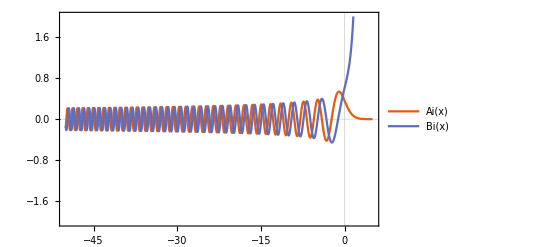

```mathematica
Plot[{AiryAi[x],AiryBi[x]},{x,-50,5},PlotRange->{-2,2},PlotTheme->"Scientific",PlotLegends->{"Ai(x)","Bi(x)"}]
```

```mathematica
ψApos[x_]= A AiryAi[(2^(1/3) m (k x-ℰ))/(k m ℏ)^(2/3)];
ψAneg[x_]= A AiryAi[(2^(1/3) m (k (-x)-ℰ))/(k m ℏ)^(2/3)];
```

```mathematica
FullSimplify[-ℏ^2/(2m)ψ''[x]+k x ψ[x]==ℰ ψ[x]/.ψ->ψApos,assump]
FullSimplify[-ℏ^2/(2m)ψ''[x]+k (- x) ψ[x]==ℰ ψ[x]/.ψ->ψAneg,assump]
```

True

True

```mathematica
ψBpos[x_]=B AiryBi[(2^(1/3) m (k x-ℰ))/(k m ℏ)^(2/3)];
ψBneg[x_]=B AiryBi[(2^(1/3) m (k (-x)-ℰ))/(k m ℏ)^(2/3)];
```

```mathematica
FullSimplify[-ℏ^2/(2m)ψ''[x]+k x ψ[x]==ℰ ψ[x]/.ψ->ψBpos,assump]
FullSimplify[-ℏ^2/(2m)ψ''[x]+k (- x) ψ[x]==ℰ ψ[x]/.ψ->ψBneg,assump]
```

True

True

```mathematica
FullSimplify[(ψApos'[x]/.x->0)==(ψAneg'[x]/.x->0)/.{ℰ->((2^(1/3) m)/(k m ℏ)^(2/3))^-1 ξ},assump]
```

AiryAiPrime[-ξ]==0

```mathematica
FullSimplify[(ψBpos'[x]/.x->0)==(ψBneg'[x]/.x->0)/.{ℰ->((2^(1/3) m)/(k m ℏ)^(2/3))^-1 ξ},assump]
```

AiryBiPrime[-ξ]==0

```mathematica
negAiPrimeZeros=Solve[AiryAiPrime[-ξ]==0&&0<ξ<40];
negBiPrimeZeros=Solve[AiryBiPrime[-ξ]==0&&0<ξ<40];
```

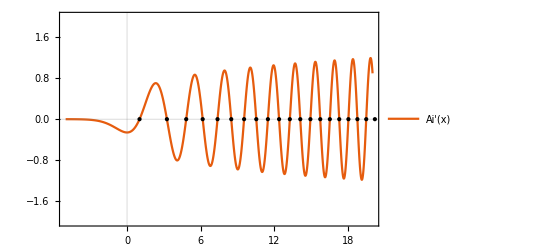

```mathematica
Plot[AiryAiPrime[-ξ],{ξ,-5,20},PlotRange->{-2,2},PlotTheme->"Scientific",PlotLegends->{"Ai'(x)"},Epilog->Style[Point[{#,AiryAiPrime[-#]}]&/@(ξ/.negAiPrimeZeros),PointSize[Large],Red]]
```

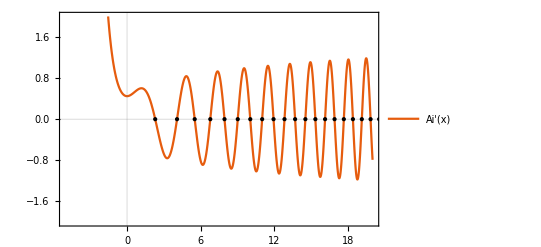

```mathematica
Plot[AiryBiPrime[-ξ],{ξ,-5,20},PlotRange->{-2,2},PlotTheme->"Scientific",PlotLegends->{"Ai'(x)"},Epilog->Style[Point[{#,AiryBiPrime[-#]}]&/@(ξ/.negBiPrimeZeros),PointSize[Large],Red]]
```

```mathematica
exactEnergies=Sort[((m/(k m ℏ)^(2/3))((2^(1/3) m)/(k m ℏ)^(2/3))^-1 ξ/.N@negAiPrimeZeros)∪((m/(k m ℏ)^(2/3))((2^(1/3) m)/(k m ℏ)^(2/3))^-1 ξ/.N@negBiPrimeZeros)]
```

{0.808617,1.8211,2.5781,3.23287,3.82572,4.37519,4.89182,5.38232,5.8513,6.30212,6.73732,7.15885,7.56829,7.96692,8.35581,8.73584,9.10776,9.47223,9.82981,10.181,10.5262,10.8659,11.2003,11.5298,11.8547,12.1751,12.4914,12.8038,13.1123,13.4173,13.7189,14.0171,14.3123,14.6044,14.8936,15.1801,15.4638,15.745,16.0237,16.3,16.574,16.8457,17.1153,17.3827,17.6481,17.9115,18.173,18.4327,18.6905,18.9465,19.2009,19.4535,19.7045,19.954,20.2019,20.4482,20.6931,20.9366,21.1786,21.4193,21.6586,21.8967,22.1334,22.3689,22.6031,22.8361,23.068,23.2987,23.5282,23.7566,23.984,24.2102,24.4355,24.6596,24.8828,25.105,25.3262,25.5464,25.7657,25.9841,26.2015,26.4181,26.6337,26.8485,27.0624,27.2755,27.4878,27.6992,27.9099,28.1197,28.3288,28.5371,28.7447,28.9515,29.1575,29.3629,29.5675,29.7714,29.9746,30.1772,30.379,30.5802,30.7807,30.9806,31.1798,31.3784,31.5764}

```mathematica
Solve[p^2/(2m)+k RealAbs[x]^β ==ℰ ,p]
```

{{p→-√2 √(m ℰ-k m RealAbs[x]^β)},{p→√2 √(m ℰ-k m RealAbs[x]^β)}}

```mathematica
Solve[√2 √(m ℰ-k m RealAbs[x])==0,x]
```

{{x→ConditionalExpression[-ℰ/k, ]},{x→ConditionalExpression[ℰ/k, ]}}

```mathematica
Integrate[√2 √(m ℰ-k m RealAbs[x]),{x,-(ℰ/k),(ℰ/k)},Assumptions->assump]
```

(4 √2 √(m ℰ^3))/(3 k)

```mathematica
FullSimplify[((9 π^2 k^2 ℏ^2)/(128m))^(1/3)(2n-1)^(2/3)==(k^(2/3) (-1+2 n)^(2/3) (3 π)^(2/3) ℏ^(2/3))/(4 2^(1/3) m^(1/3)),assump]
```

True

```mathematica
2Integrate[√2 √(m ℰ-k m x^β),{x,0,(ℰ/k)^(1/β)},Assumptions->assump]
```

(√(2 π) (ℰ/k)^(1/β) √(m ℰ) Gamma[1+1/β])/Gamma[3/2+1/β]

```mathematica
Solve[2(√(π/2) (ℰ/k)^(1/β) √(m ℰ) Gamma[1+1/β])/Gamma[3/2+1/β]==π ℏ (n+1/2),ℰ]
```

{{ℰ→(2 π)^(-1/(2 (1/2+1/β))) (-(k^(1/β) (-(π ℏ)/2-n π ℏ) Gamma[3/2+1/β])/(√m Gamma[1+1/β]))^((2 β)/(2+β))}}

```mathematica
FullSimplify[(2 π)^(-1/(2 (1/2+1/β))) (-(k^(1/β) (-(π ℏ)/2-n π ℏ) Gamma[3/2+1/β])/(√m Gamma[1+1/β]))^((2 β)/(2+β))== (√(π/8)(ℏ k^(1/β))/(√m)(1+2 n)Gamma[3/2+1/β]/Gamma[1+1/β])^(β/(1+β/2)),assump]
```

True

```mathematica
2(√(π/2) (ℰ/k)^(1/β) √(m ℰ) Gamma[1+1/β])/Gamma[3/2+1/β]/.β->1
```

(4 √2 ℰ √(m ℰ))/(3 k)

```mathematica
Solve[(4 √2 √(m ℰ^3))/(3 k)==(n+1/2)π ℏ,ℰ]
```

{{ℰ→(k^(2/3) (1+2 n)^(2/3) (-3 π)^(2/3) ℏ^(2/3))/(4 2^(1/3) m^(1/3))},{ℰ→-((-1/2)^(1/3) k^(2/3) (1+2 n)^(2/3) (3 π)^(2/3) ℏ^(2/3))/(4 m^(1/3))},{ℰ→(k^(2/3) (1+2 n)^(2/3) (3 π)^(2/3) ℏ^(2/3))/(4 2^(1/3) m^(1/3))}}

```mathematica
FullSimplify[((ℏ^(2/3)k^(2/3))/m^(1/3))^-1(k^(2/3) (1+2 n)^(2/3) (3 π)^(2/3) ℏ^(2/3))/(4 2^(1/3) m^(1/3)),assump]
```

((1+2 n)^(2/3) (3 π)^(2/3))/(4 2^(1/3))

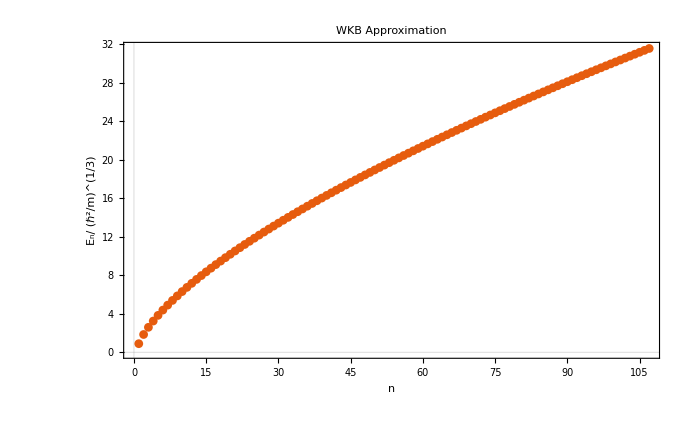

```mathematica
ListPlot[Table[((1+2 n)^(2/3) (3 π)^(2/3))/(4 2^(1/3)),{n,0,Length[exactEnergies]-1}],PlotTheme->"Scientific",FrameLabel->{"n"," E_n/ (ℏ^2/m)^(1/3)"},PlotLabel->"WKB Approximation"]
```

```mathematica
FullSimplify[D[((9 π^2 κ^2 ℏ^2)/(128 m))^(1/3)(2n-1)^(2/3),n]^-1==(6/π^2 m/(κ^2 ℏ^2))^(1/3)(2 n-1)^(1/3),n>0&&κ>0&&ℏ>0&&m>0]
```

True

```mathematica
ClearAll[m]
```

```mathematica
Solve[(κ^2 ℏ^2/m)^(1/3)==EE,κ]
```

{{κ→-(EE^(3/2) √m)/ℏ},{κ→(EE^(3/2) √m)/ℏ}}

```mathematica
UnitConvert[Quantity[("ElectronMass")/("ReducedPlanckConstant")^2],]
```

$Failed

```mathematica
(("Electronvolts")/("Meters"))^2("ReducedPlanckConstant")^2/"ElectronMass"
```

```mathematica
UnitConvert[Quantity[(("Electronvolts")/("Meters"))^2("ReducedPlanckConstant")^2/"ElectronMass"]^(1/3)]
```

6.79247483×10^-26 kg m^2/s^2

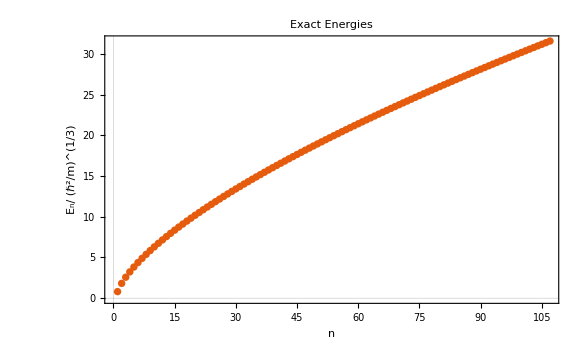

```mathematica
ListPlot[exactEnergies,PlotTheme->"Scientific",FrameLabel->{"n"," E_n/ (ℏ^2/m)^(1/3)"},PlotLabel->"Exact Energies"]
```

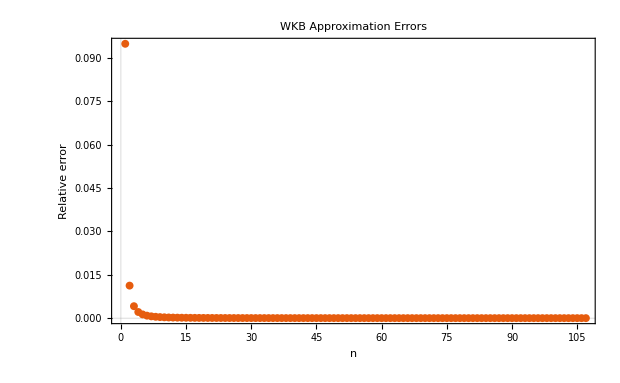

```mathematica
ListPlot[Abs[Table[((1+2 n)^(2/3) (3 π)^(2/3))/(4 2^(1/3)),{n,0,Length[exactEnergies]-1}]-exactEnergies]/exactEnergies,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"n","Relative error"},PlotLabel->"WKB Approximation Errors"]
```

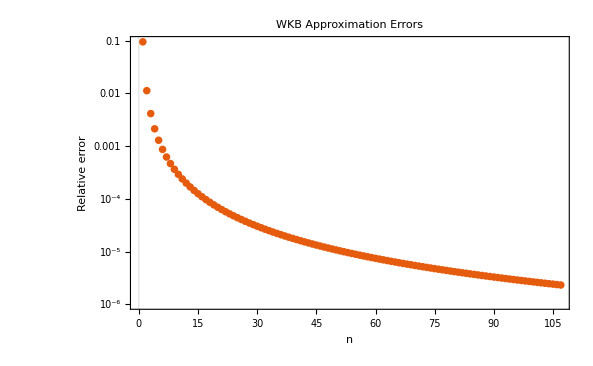

```mathematica
ListLogPlot[Abs[Table[((1+2 n)^(2/3) (3 π)^(2/3))/(4 2^(1/3)),{n,0,Length[exactEnergies]-1}]-exactEnergies]/exactEnergies,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"n","Relative error"},PlotLabel->"WKB Approximation Errors"]
```

```mathematica
Table[((1+2 n)^(2/3) (3 π)^(2/3))/(4 2^(1/3)),{n,0,Length[exactEnergies]-1}]//N
```

{0.885341,1.84158,2.58875,3.23973,3.83065,4.37898,4.89485,5.38483,5.85342,6.30396,6.73892,7.16027,7.56956,7.96807,8.35685,8.73679,9.10864,9.47304,9.83057,10.1817,10.5269,10.8665,11.2009,11.5304,11.8552,12.1756,12.4919,12.8042,13.1128,13.4177,13.7193,14.0175,14.3126,14.6047,14.894,15.1804,15.4641,15.7453,16.024,16.3003,16.5743,16.846,17.1155,17.383,17.6483,17.9118,18.1733,18.4329,18.6907,18.9467,19.2011,19.4537,19.7047,19.9542,20.202,20.4484,20.6933,20.9368,21.1788,21.4195,21.6588,21.8968,22.1335,22.369,22.6032,22.8363,23.0681,23.2988,23.5283,23.7568,23.9841,24.2104,24.4356,24.6598,24.8829,25.1051,25.3263,25.5465,25.7658,25.9842,26.2016,26.4182,26.6338,26.8486,27.0625,27.2756,27.4879,27.6993,27.91,28.1198,28.3289,28.5372,28.7448,28.9516,29.1576,29.3629,29.5676,29.7715,29.9747,30.1772,30.3791,30.5803,30.7808,30.9807,31.1799,31.3785,31.5765}

```mathematica
exactEnergies
```

{0.808617,1.8211,2.5781,3.23287,3.82572,4.37519,4.89182,5.38232,5.8513,6.30212,6.73732,7.15885,7.56829,7.96692,8.35581,8.73584,9.10776,9.47223,9.82981,10.181,10.5262,10.8659,11.2003,11.5298,11.8547,12.1751,12.4914,12.8038,13.1123,13.4173,13.7189,14.0171,14.3123,14.6044,14.8936,15.1801,15.4638,15.745,16.0237,16.3,16.574,16.8457,17.1153,17.3827,17.6481,17.9115,18.173,18.4327,18.6905,18.9465,19.2009,19.4535,19.7045,19.954,20.2019,20.4482,20.6931,20.9366,21.1786,21.4193,21.6586,21.8967,22.1334,22.3689,22.6031,22.8361,23.068,23.2987,23.5282,23.7566,23.984,24.2102,24.4355,24.6596,24.8828,25.105,25.3262,25.5464,25.7657,25.9841,26.2015,26.4181,26.6337,26.8485,27.0624,27.2755,27.4878,27.6992,27.9099,28.1197,28.3288,28.5371,28.7447,28.9515,29.1575,29.3629,29.5675,29.7714,29.9746,30.1772,30.379,30.5802,30.7807,30.9806,31.1798,31.3784,31.5764}

```mathematica
ℰ//TeXForm
```

\mathcal{E}